# Projections

```mathematica
ψ = Sum[c[G]*Exp[ⅈGr],G]/Sqrt[vol];
```

5.

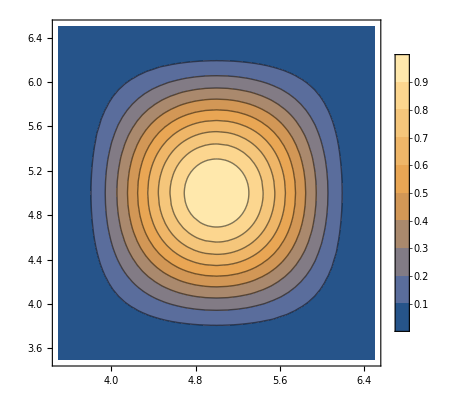

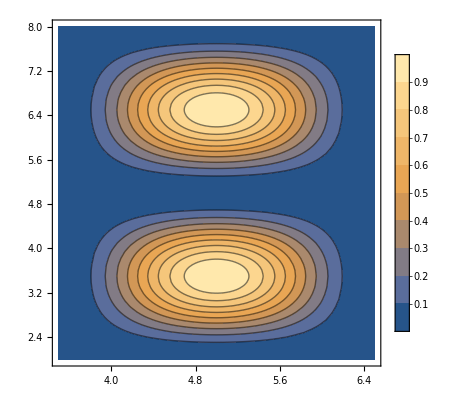

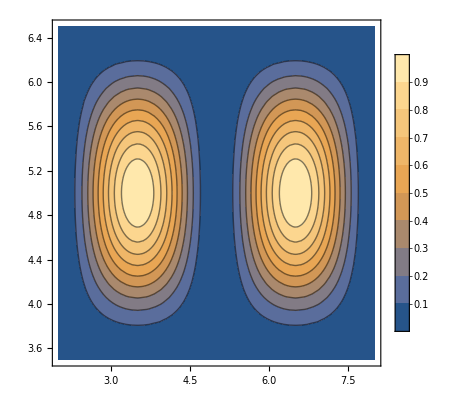

```mathematica
(*Trial Orbitals*)
Clear[L,k];

g1[x_,y_]:=Sin[κ*(x-xc)]*Sin[κ*(y-yc)];
g2[x_,y_]:=Sin[κ*(x-xc)]*Cos[κ*(y-yc)];
g3[x_,y_]:=Cos[κ*(x-xc)]*Sin[κ*(y-yc)];
(*Plane wave basis function (c.c.)*)
basVec[x_,y_,Gx_,Gy_]:= Exp[-ⅈ*(Gx*x+Gy*y)]/Sqrt[vol];

(*Plotting of trial orbitals*)
atC=5.0
atR=1.5;
κ=π/(2*atR);
xc=atC-atR;
yc=atC-atR;

ContourPlot[g1[x,y]^2,{x,atC-atR,atC+atR},{y,atC-atR,atC+atR},PlotLegends->Automatic]
ContourPlot[g2[x,y]^2,{x,atC-atR,atC+atR},{y,atC-2*atR,atC+2*atR},PlotLegends->Automatic]
ContourPlot[g3[x,y]^2,{x,atC-2*atR,atC+2*atR},{y,atC-atR,atC+atR},PlotLegends->Automatic]

(*Integrals*)
Clear[κ];
Clear[Gx,Gy,xc,yc];
f1[Gx_,Gy_]:= Integrate[basVec[x,y,Gx,Gy]*g1[x,y],{x,xL,xR},{y,yL,yR}];
f2[Gx_,Gy_]:= Integrate[basVec[x,y,Gx,Gy]*g2[x,y],{x,xL,xR},{y,yL,yR}];
f3[Gx_,Gy_]:= Integrate[basVec[x,y,Gx,Gy]*g3[x,y],{x,xL,xR},{y,yL,yR}];

(*f2[Gx,Gy]*)
```

## 3 Trial Orbitals per well